```mathematica
(* taken from wolfram demos for binomial confidence intervals: http://demonstrations.wolfram.com/ConfidenceIntervalsForTheBinomialDistribution *)
```

```mathematica
(* j is successes, n is trials (attempts, samples ), p is probably the confidence? *) 
b[j_,n_,p_]:=CDF[BinomialDistribution[n,p],j];
intervals[jj_,nn_,confLvl_, opts___]:=Module[{t025=Quantile[NormalDistribution[],1 - (1-confLvl)/2],
blueSquare=Graphics[{Blue,Rectangle[]},ImageSize->10],redSquare=Graphics[{Red,Rectangle[]},ImageSize->10],blackSquare=Graphics[{Black,Rectangle[]},ImageSize->10],izq,der,interWald,interWilson,nums,int1,int2,int3,std,corrnums,stimes},
izq=Quiet@If[jj==1,0,(p/.NSolve[1-b[jj-1,nn,p]==(1-confLvl)/2,p])[[1]]];der=Quiet@(p/.NSolve[b[jj,nn,p]==(1-confLvl)/2,p])[[1]];
interWald=Max[0,#]&/@{jj/nn -t025  √(jj/nn (1-jj/nn)/nn),jj/nn +t025  √(jj/nn (1-jj/nn)/nn)};
interWilson={1/(1+t025^2/nn)(jj/nn+1/(2 nn) t025^2-t025 √((jj/nn (1-jj/nn))/nn+t025^2/(4 nn^2))),1/(1+t025^2/nn)(jj/nn+1/(2 nn) t025^2+t025 √((jj/nn (1-jj/nn))/nn+t025^2/(4 nn^2)))};int1=interWald;
int2=interWilson;
int3={izq,der};nums={interWald,interWilson,{izq,der}};
std=StringDrop[#,1]&/@(ToString/@(PaddedForm[#,{3,3}]&/@Flatten[nums]));difs=#[[2]]-#[[1]]&/@nums;
az=StringDrop[#,1]&/@(ToString/@(PaddedForm[#,{3,3}]&/@difs));
corrnums=Table["["<>std[[j]]<>","<>" "<>std[[j+1]]<>"]",{j,1,Length[std]-1,2}];stimes=Text[#]&/@Table[corrnums[[j]]<>"      "<>az[[j]],{j,1,3}];
ListLinePlot[{{jj/nn,0},{jj/nn,0.003}},Axes->{True,False},AxesOrigin->{0.25,0},PlotStyle->{Black,Thickness[0.001]},PlotRange->{{0,1},{-0.002,0.009}},Epilog->{Text[Style["j/n",Italic,Medium],{jj/nn,-0.00075}],Inset[Grid[{{Style[StringJoin[ToString[confLvl*100],"% confidence intervals"],Medium]},{Style["for the probability parameter",Medium]},{Style["in a binomial distribution",Medium]}}],{0.5,0.008}],Inset[Grid[{{Text["method"],Text[""],Text["  interval           length"]},{Text["conventional"],blueSquare,stimes[[1]]},{Text["Wilson"],redSquare,stimes[[2]]},{Text["Clopper-Pearson"],blackSquare,stimes[[3]]}}],{0.5,0.005}],Thick,Blue,Line@MapThread[List,{int1,{0.003,0.003}}],Thick,Red,Line@MapThread[List,{int2,{0.002,0.002}}],Thick,Black,Line@MapThread[List,{int3,{0.001,0.001}}]},opts]]
```

```mathematica
Manipulate[
If[successes>tries-2,successes=tries-2];
intervals[successes,tries,confidence, ImageSize->550],
{{successes,10},1,tries-2,1,Appearance->"Labeled"},
{{tries,50},20,200,5,Appearance->"Labeled"},{{confidence,0.95},0.5,0.99,0.01,Appearance->"Labeled"},SaveDefinitions->True]
```

```mathematica
(* redefining Wald CI for convenience *) 
interWald[jj_, nn_,confLvl_]:=With[{t025=Quantile[NormalDistribution[],1 - (1-confLvl)/2]},Interval[Max[0,#]&/@{jj/nn -t025  √(jj/nn (1-jj/nn)/nn),jj/nn +t025  √(jj/nn (1-jj/nn)/nn)}]];
```

```mathematica
(* redefining Wilson CI for convenience *) 
interWilson[jj_, nn_,confLvl_]:=With[{t025=Quantile[NormalDistribution[],1 - (1-confLvl)/2]}, Interval[{1/(1+t025^2/nn)(jj/nn+1/(2 nn) t025^2-t025 √((jj/nn (1-jj/nn))/nn+t025^2/(4 nn^2))),1/(1+t025^2/nn)(jj/nn+1/(2 nn) t025^2+t025 √((jj/nn (1-jj/nn))/nn+t025^2/(4 nn^2)))}]]
```

```mathematica
(*** FILE MANIPULATIONS ***)
```

```mathematica
(* useful def*)
dataDirPath = "~/Dropbox/upenn/research/aa/monitoring_data/data/Session_4_Sonar_Nocontroller_8Aug2019/";
```

```mathematica
monFilenames[winSize_, idpairlist_] := StringJoin[dataDirPath, "Iteration_", ToString[#[[1]]], "/mon", ToString[#[[2]]], "_",ToString[winSize], "/iter", ToString[#[[1]]], "_mondet", ToString[#[[2]]], "_",ToString@winSize, "_estrates.txt"] & /@idpairlist;

allMonFilenames[winSize_] := StringJoin[dataDirPath, "Iteration_", ToString[#[[1]]], "/mon", ToString[#[[2]]], "_",ToString[winSize], "/iter", ToString[#[[1]]], "_mondet", ToString[#[[2]]], "_",ToString@winSize, "_estrates.txt"] & /@Flatten[Outer[List, Range[1,5], Range[1,5]], 1];

detFilenames[idpairlist_] := StringJoin[dataDirPath, "Iteration_", ToString[#[[1]]], "/det", ToString[#[[2]]], "/iter", ToString[#[[1]]], "_both_det_estrates.txt"] & /@idpairlist;

allDetFilenames = StringJoin[dataDirPath, "Iteration_", ToString[#[[1]]], "/det", ToString[#[[2]]], "/iter", ToString[#[[1]]], "_both_det_estrates.txt"] & /@Flatten[Outer[List, Range[1,5], Range[1,5]], 1];

(* add up a given field's values over filenames *) 
countFromFiles[fieldName_, filenames_] := Plus@@(*list of frame numbers from each*)(getValueFromListOfPairs[#,fieldName]& /@ (*list of all stat dicts*) (nameValuePairsFromFile/@filenames(*list of filenames*)))
```

```mathematica
(*** TESTING WILSON CONFIDENCE INTERVALS: data-driven CI for detector FPR vs ground truth of 0.1 ***)
```

```mathematica
(* a pair of interval (based by pairlist) and GT *)
oneIntervalDetFPRGtTestPairWilson[pairIdList_] := {(* interval *) interWilson[countFromFiles[ "FPcount",detFilenames[pairIdList]], countFromFiles[ "h0count",detFilenames[pairIdList]], 0.95], (* prediction *)  0.1};

oneIntervalDetFPRGtTestWilson[pairIdList_] := IntervalMemberQ[(* interval *) interWilson[countFromFiles[ "FPcount",detFilenames[pairIdList]], countFromFiles[ "h0count",detFilenames[pairIdList]], 0.95], (* prediction *) 0.1];
```

```mathematica
(* fixed sampling of subsets, samplect for each. Returns counts of Trues for each subset size *) 
generateDetFPRGtSuccessCountsPerSubsetSizeWilson[samplect_]:= With[{subsetsCt = #},
(* count truths *)Count[oneIntervalDetFPRGtTestWilson[#]&/@ (* all possible sets of pairs for tests *) Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {subsetsCt},{#}] &/@ (* getting samplect random subsets *)  RandomInteger[{1,(*counting subsets *)Length@Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {subsetsCt}]
},samplect], {True}]
]& /@ Range[1, 24];
```

```mathematica
generateDetFPRGtSuccessCountsPerSubsetSizeWilson[1000]
```

```mathematica
resListDetFPRGt1000= {965,922,926,927,939,947,943,946,936,942,925,940,945,948,955,967,972,989,983,990,1000,1000,1000,1000};
```

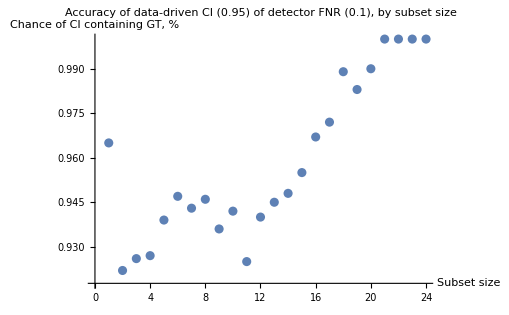

```mathematica
(* 1k samples per fixed subset, wilson underperforming *) 
ListPlot[Inner[List, Range[1,24], resListDetFPRGt1000/1000, List], AxesLabel->{"Subset size", "Chance of CI containing GT, %"}, PlotLabel->"Accuracy of data-driven CI (0.95) of detector FNR (0.1), by subset size"]
```

```mathematica
(** not-tied-to-subset-size sampling below **) 
(* a list of pairs {subset size, whether CI contains the prediciton} *) 
generateDetFPRvsCISampleWilson[sampleCt_]:= ({#[[1]],oneIntervalDetFPRGtTestWilson[#[[2]]]}&/@( Flatten[{Length@#, #} &/@(* list of lists of subsets possible sets of pairs for tests *) Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {1,25},{#}] &/@ (* getting random 100 subsets *)  RandomInteger[{1,(*all subsets *)subsetCt
},sampleCt],1]));

(* triples of {subsetsize, # of trues at that size, # of falses at that size} *)
tallyUpDetFPRvsCISample[sample_]:= With[ {trueCt= Count[sample, {#, True}], falseCt= Count[sample, {#, False}]} , {#,trueCt, falseCt}]& /@  Range[1,25];

(* converting tallied triples to ratios and stdev, getting pairs {subset size, accuracy w/uncert based on wilson CIs} *) 
generateDetFPRvsCIOutcomesWilson[sampleCt_]:={(*subset size*) #[[1]], (*ratio of successes to total *) With[{est = #[[2]]/(#[[2]]+#[[3]]), int = interWilson[#[[2]],#[[2]]+#[[3]], 0.95]},Around[(*estimated accuracy*)est,(* converting wilson interval to uncertainty bounds*) {Min@int-est, Max@int-est}]] }&/@ (* getting tallied sample data and filtering it*)Select[tallyUpDetFPRvsCISample[generateDetFPRvsCISampleWilson[sampleCt]], #[[2]] >0 ∨ #[[3]]>0 # &];
```

```mathematica
generateDetFPRvsCIOutcomes[10000]
```

```mathematica
randomOutcomesDetFPR10000Wilson= {{1,1.000000000000000000.80.00000000000000022},{3,1.000000000000000000.60.00000000000000022},{4,1.000000000000000000.60.00000000000000022},{5,1.000000000000000000.320.00000000000000022},{6,0.9600.090.029},{7,0.9460.050.028},{8,0.9510.0290.019},{9,0.9490.0210.015},{10,0.9410.0160.013},{11,0.9300.0150.013},{12,0.9400.0130.010},{13,0.9570.0110.009},{14,0.9510.0130.010},{15,0.9540.0150.012},{16,0.9640.0180.012},{17,0.9690.0240.014},{18,0.9810.040.013},{19,1.000000000000000000.080.00000000000000022},{20,1.000000000000000000.180.00000000000000022},{21,0.830.40.14},{22,1.000000000000000000.70.00000000000000022},{23,1.000000000000000000.80.00000000000000022}};
```

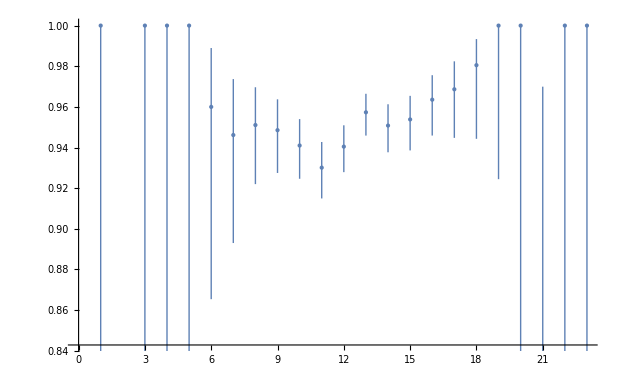

```mathematica
(* 10k random, still falling through in the middle *) 
ListPlot[randomOutcomesDetFPR10000, PlotStyle->PointSize[Large]]
```

```mathematica
generateDetFPRvsCIOutcomes[100000]
```

```mathematica
randomOutcomesDetFPR100000Wilson  = {{3,1.000000000000000000.300.00000000000000022},{4,0.940.100.04},{5,0.9290.050.031},{6,0.9350.0250.018},{7,0.9420.0140.011},{8,0.9370.0090.008},{9,0.9340.0060.006},{10,0.9400.0050.005},{11,0.9450.0040.004},{12,0.94620.0040.0034},{13,0.95100.00350.0033},{14,0.95520.0040.0034},{15,0.9570.0040.004},{16,0.9640.0050.004},{17,0.9720.0060.005},{18,0.9750.0090.007},{19,0.9840.0150.008},{20,0.9830.0320.011},{21,1.000000000000000000.080.00000000000000022},{22,1.000000000000000000.280.00000000000000011},{23,1.000000000000000000.70.00000000000000022}};
```

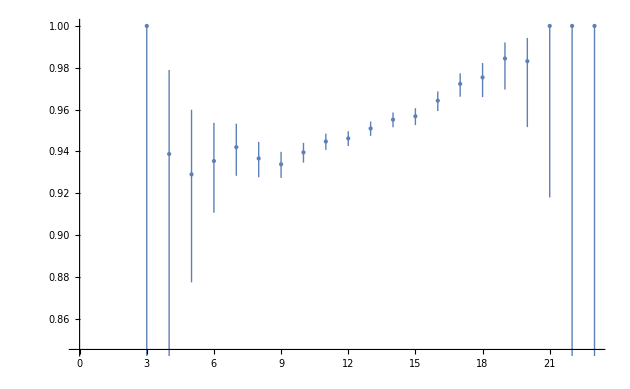

```mathematica
(* 100k random, pretty robust evidence of how the confidence intervals are underperforming *)
ListPlot[randomOutcomesDetFPR100000Wilson, PlotStyle->PointSize[Large]]
```

```mathematica
(*** TESTING WALD CONFIDENCE INTERVALS ***)
```

```mathematica
(* a pair of interval (based by pairlist) and GT *)
oneIntervalDetFPRGtTestPairWald[pairIdList_] := {(* interval *) interWald[countFromFiles[ "FPcount",detFilenames[pairIdList]], countFromFiles[ "h0count",detFilenames[pairIdList]], 0.95], (* prediction *)  0.1};

oneIntervalDetFPRGtTestWald[pairIdList_] := IntervalMemberQ[(* interval *) interWald[countFromFiles[ "FPcount",detFilenames[pairIdList]], countFromFiles[ "h0count",detFilenames[pairIdList]], 0.95], (* prediction *) 0.1];
```

```mathematica
(* fixed sampling of subsets, samplect for each. Returns counts of Trues for each subset size *) 
generateDetFPRGtSuccessCountsPerSubsetSizeWald[samplect_]:= With[{subsetsCt = #},
(* count truths *)Count[oneIntervalDetFPRGtTestWald[#]&/@ (* all possible sets of pairs for tests *) Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {subsetsCt},{#}] &/@ (* getting samplect random subsets *)  RandomInteger[{1,(*counting subsets *)Length@Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {subsetsCt}]
},samplect], {True}]
]& /@ Range[1, 24];
```

```mathematica
generateDetFPRGtSuccessCountsPerSubsetSizeWald[1000]
```

```mathematica
resListDetFPRGt1000Wald= {844,940,951,956,968,965,975,976,958,970,974,978,972,973,984,992,991,990,995,1000,1000,1000,1000,1000};
```

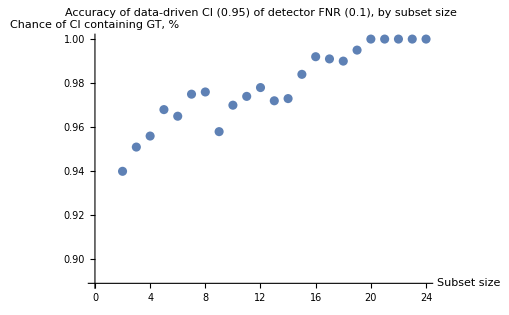

```mathematica
ListPlot[Inner[List, Range[1,24], resListDetFPRGt1000Wald/1000, List], AxesLabel->{"Subset size", "Chance of CI containing GT, %"}, PlotLabel->"Accuracy of data-driven CI (0.95) of detector FNR (0.1), by subset size"]
```

```mathematica
(** not-tied-to-subset-size sampling below **) 
(* a list of pairs {subset size, whether CI contains the prediciton} *) 
generateDetFPRvsCISampleWald[sampleCt_]:= ({#[[1]],oneIntervalDetFPRGtTestWald[#[[2]]]}&/@( Flatten[{Length@#, #} &/@(* list of lists of subsets possible sets of pairs for tests *) Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {1,25},{#}] &/@ (* getting random 100 subsets *)  RandomInteger[{1,(*all subsets *)subsetCt
},sampleCt],1]));

(* triples of {subsetsize, # of trues at that size, # of falses at that size} *)
tallyUpDetFPRvsCISample[sample_]:= With[ {trueCt= Count[sample, {#, True}], falseCt= Count[sample, {#, False}]} , {#,trueCt, falseCt}]& /@  Range[1,25];

(* converting tallied triples to ratios and stdev, getting pairs {subset size, accuracy w/uncert based on Wald CIs} *) 
generateDetFPRvsCIOutcomesWald[sampleCt_]:={(*subset size*) #[[1]], (*ratio of successes to total *) With[{est = #[[2]]/(#[[2]]+#[[3]]), int = interWald[#[[2]],#[[2]]+#[[3]], 0.95]},Around[(*estimated accuracy*)est,(* converting Wald interval to uncertainty bounds*) {Min@int-est, Max@int-est}]] }&/@ (* getting tallied sample data and filtering it*)Select[tallyUpDetFPRvsCISample[generateDetFPRvsCISampleWald[sampleCt]], #[[2]] >0 ∨ #[[3]]>0 # &];
```

```mathematica
generateDetFNRvsCIOutcomesWald[100000]
```

```mathematica
randomOutcomesDetFPR100000Wald  ={{2,1.000000000000000001122},{3,1.000000000000000001122},{4,0.970.050.05},{5,0.9870.0180.018},{6,0.9580.0170.017},{7,0.9650.0100.010},{8,0.9710.0060.006},{9,0.9630.0050.005},{10,0.97290.00320.0032},{11,0.97130.00280.0028},{12,0.97370.00250.0025},{13,0.97630.00240.0024},{14,0.97800.00250.0025},{15,0.98100.00270.0027},{16,0.98550.00300.0030},{17,0.99030.00340.0034},{18,0.9930.0050.005},{19,0.9980.0040.004},{20,1.000000000000000001122},{21,1.000000000000000001122},{22,1.000000000000000001122}};
```

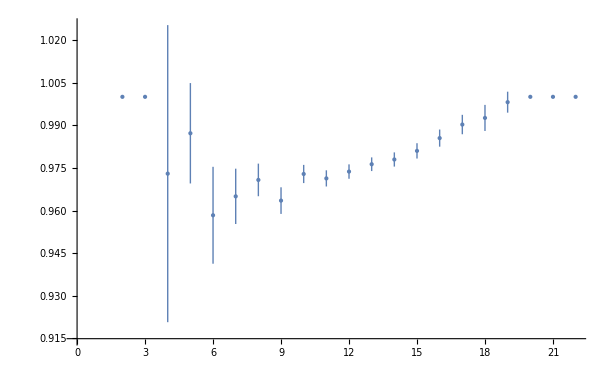

```mathematica
(* somehow wald intervals perform better -- perhaps use them? *) 
ListPlot[randomOutcomesDetFPR100000Wald, PlotStyle->PointSize[Large]]
```

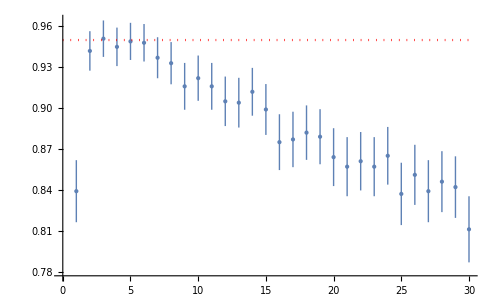
```mathematica
(*** TESTING DETECTOR WITH REPLACEMENT ***) 

fpr1000sampleChartDataWilson = {{1,0.8390.0230.023},{2,0.9420.0140.014},{3,0.9510.0130.013},{4,0.9450.0140.014},{5,0.9490.0140.014},{6,0.9480.0140.014},{7,0.9370.0150.015},{8,0.9330.0150.015},{9,0.9160.0170.017},{10,0.9220.0170.017},{11,0.9160.0170.017},{12,0.9050.0180.018},{13,0.9040.0180.018},{14,0.9120.0180.018},{15,0.8990.0190.019},{16,0.8750.0200.020},{17,0.8770.0200.020},{18,0.8820.0200.020},{19,0.8790.0200.020},{20,0.8640.0210.021},{21,0.8570.0220.022},{22,0.8610.0210.021},{23,0.8570.0220.022},{24,0.8650.0210.021},{25,0.8370.0230.023},{26,0.8510.0220.022},{27,0.8390.0230.023},{28,0.8460.0220.022},{29,0.8420.0230.023},{30,0.8110.0240.024}};
Show[ListPlot[fpr1000sampleChartDataWilson, PlotStyle->PointSize[Medium]], chart95conf[30]]
-Graphics-
```

```mathematica
(* back to fixed attempts per subset, now sessions 4 and 5: *)
```

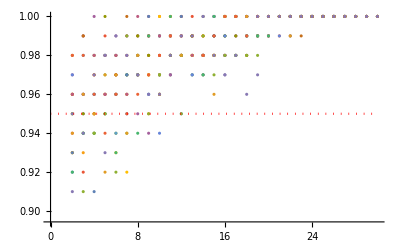

```mathematica
Show[ListPlot@Table[generateSuccessCtsPerSubsetSizeForCharting[pairingGtDetFPR, {4,5}, (*monwin size, ignored in this case*) 10, (* attempts per dot *) 100],(* number of series *) 20],chart95conf[30]]
```

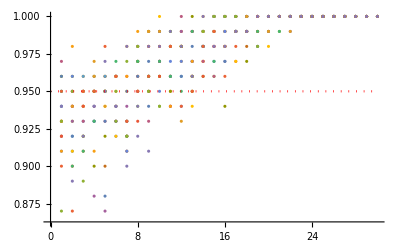

```mathematica
Show[ListPlot@Table[generateSuccessCtsPerSubsetSizeForCharting[pairingGtDetFNR, {4,5}, (*monwin size, ignored in this case*) 10, (* attempts per dot *) 100],(* number of series *) 20],chart95conf[30]]
```

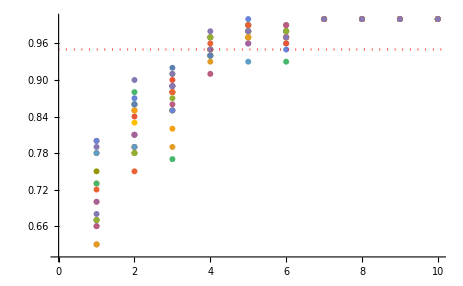
```mathematica
(* now only on datasets without redundant detectors: *) 

Show[ListPlot@Table[generateSuccessCtsPerSubsetSizeForCharting[pairingGtDetFPR,fullTripleListNoRedun, {4,5}, (*monwin size, ignored in this case*) 10, (* attempts per dot *)100],(* number of series *) 20],chart95conf[30]] 
-Graphics-
```

```mathematica
(* same as above for 6 sessions *)
```

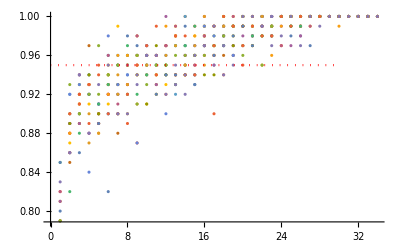

```mathematica
Show[ListPlot@Table[generateSuccessCtsPerSubsetSizeForCharting[pairingGtDetFPR,fullTripleListNoRedun, {4,5,6}, (*monwin size, ignored in this case*) 10, (* attempts per dot *)100],(* number of series *) 20],chart95conf[30]]
```

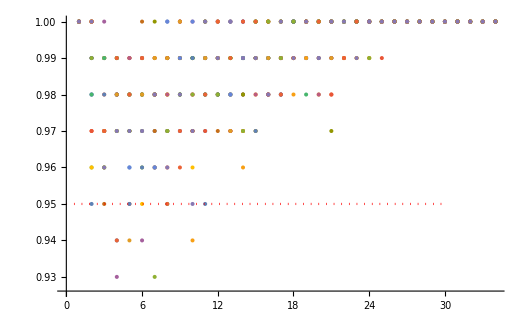

```mathematica
Show[ListPlot@Table[generateSuccessCtsPerSubsetSizeForCharting[pairingGtDetFNR,fullTripleListNoRedun, {4,5,6}, (*monwin size, ignored in this case*) 10, (* attempts per dot *)100],(* number of series *) 20],chart95conf[30]]
```

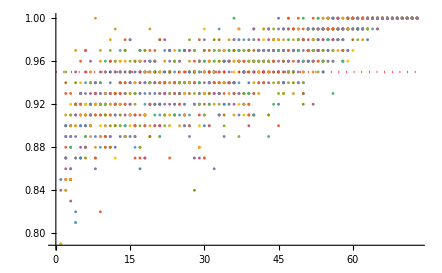
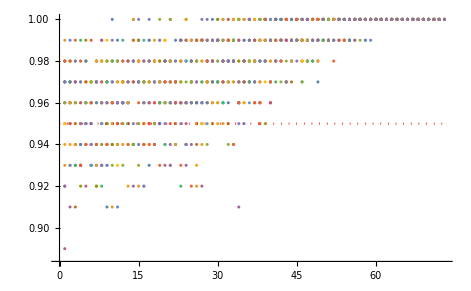
```mathematica
(* same as above for 7 sessions *) 

Show[ListPlot@Table[generateSuccessCtsPerSubsetSizeForCharting[pairingGtDetFPR,fullTripleListNoRedun, {4,5,6,7}, (*monwin size, ignored in this case*) 10, (* attempts per dot *)100],(* number of series *) 20],chart95conf[73]] 
-Graphics-

Show[ListPlot@Table[generateSuccessCtsPerSubsetSizeForCharting[pairingGtDetFNR,fullTripleListNoRedun, {4,5,6,7}, (*monwin size, ignored in this case*) 10, (* attempts per dot *)100],(* number of series *) 20],chart95conf[73]] 
-Graphics-

(** for fully disjoint partitions DET FPR -- too little data **) 
generatePartitionOutcomesForCharting[pairingGtDetFPR, {4,5}, 25, 10, interWald, interWilson]
```

{{1,0.830.170.09},{2,1.00000000000000000.200.0000000000000004},{3,1.000000000000000000.280.00000000000000011},{4,1.000000000000000000.350.00000000000000022},{5,10.40.},{6,1.000000000000000000.40.00000000000000022},{7,1.000000000000000000.50.00000000000000022},{8,1.000000000000000000.60.00000000000000022},{9,1.000000000000000000.60.00000000000000022},{10,1.000000000000000000.60.00000000000000022},{11,1.000000000000000000.70.00000000000000022},{12,1.000000000000000000.70.00000000000000022},{13,1.000000000000000000.70.00000000000000022},{14,1.000000000000000000.70.00000000000000022},{15,1.000000000000000000.70.00000000000000022},{16,1.000000000000000000.80.00000000000000022},{17,1.000000000000000000.80.00000000000000022},{18,1.000000000000000000.80.00000000000000022},{19,1.000000000000000000.80.00000000000000022},{20,1.000000000000000000.80.00000000000000022},{21,1.000000000000000000.80.00000000000000022},{22,1.000000000000000000.80.00000000000000022},{23,1.000000000000000000.80.00000000000000022},{24,1.000000000000000000.80.00000000000000022},{25,1.000000000000000000.80.00000000000000022}}